## Setup

```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
DATADIR = FileNameJoin[ParentDirectory[], "/data/raw"] ;

CreateMatrix[nn_, mm_]:=Module[{J,vars,i},(*Variables du système*)
vars=Join[Table[H[i],{i,1,nn}],{H2},Table[P[i],{i,1,mm}],{P2}];

(*Initialiser la matrice jacobienne avec des zéros*)
J=ConstantArray[0,{nn+mm+2,nn+mm+2}];

(*Remplissage de la sous-matrice pour H[i]*)
Do[J[[i,i]]=-θH-δH1-a P2[t];
If[i>1,J[[i,i-1]]=θH],{i,1,nn}];
(*Remplissage des termes de parasitisme*)
Do[J[[i,nn+mm+2]]=-a*H[i][t],{i,1,nn}];
(*Termes liés à H2*)
J[[1,nn+1]]=r;
(*H1 dépend de H2*)
J[[nn+1,nn]]=θH;
(*H2 dépend de H[k]*)
J[[nn+1,nn+1]]=-δH2;


(*Remplissage de la sous-matrice pour P[i]*)Do[J[[nn+1+i,nn+1+i]]=-θP-δP1;
If[i>1,J[[nn+1+i,nn+i]]=θP],{i,1,mm}];
(*Remplissage des termes de parasitisme*)
Do[J[[nn+2,i]]=a  P2[t],{i,1,nn}];
J[[nn+2, nn+mm+2]] = a*H1[t];
(*Ligne de P2*)
J[[nn+mm+2,nn+mm+1]]=θP;
J[[nn+mm+2,nn+mm+2]]=-δP2;

(*Retourner la matrice jacobienne*)
J];
```

## Test : calcul de la courbe en fonction de tP1 (=τ2)

```mathematica
τ2Min=0.011;
τ2Max=1;
τ2Pas=0.02;

CourbeLimite={};
For[t2=τ2Max,t2>τ2Min,t2-=τ2Pas,
Module[{tsol},
(*Print["t2 = ",t2];*)
tsol=Check[ta/. FindRoot[VP[ta,t2],{ta,0.01,5},Method->"Brent"],"Failed"]; (*Use Quiet to suppress warnings,Check to handle failures*)
If[NumericQ[tsol]&&tsol>0,
AppendTo[CourbeLimite,{tsol,t2}]
(*Print["Skipping t2 = ",t2," (FindRoot failed)"]*)]
]
];
CourbeLimite
```

General::munfl: 1/203.527^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

{}

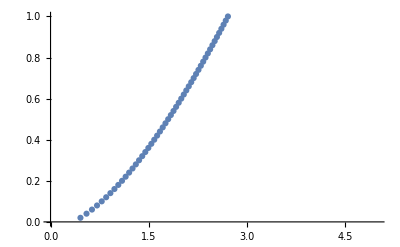

```mathematica
ListPlot[CourbeLimite,
PlotRange->{{0,5},{0,1}}]
```

## Automated script

## Parameters

```mathematica
mH1par = 1;
δH1par = 0;

δP1par = 1;
δP2par = 8;

ρpar = 33;
apar = 1;
paramsplot = {mH->mH1par, δH1->δH1par, δP1->δP1par, δP2->δP2par, ρ->ρpar, a-> apar,δH2 -> 1/tH2, mP -> 1/tP1 }

nValues={1,5,10,50,100}
mValues={1,5,10,50,100}
```

{mH→1,δH1→0,δP1→1,δP2→8,ρ→33,a→1,δH2→1/tH2,mP→1/tP1}

{1,5,10,50,100}

{1,5,10,50,100}

## Script

```mathematica
paramInfo=StringJoin["rho_",ToString[ρ/.paramsplot],
"_dH1_",ToString[δH1/.paramsplot],
"_dP2_",ToString[δP2/.paramsplot],
"_dP1_",ToString[δP1/.paramsplot]];
Folder="Murdoch_stability_n_m_tH2-tP1_"<>paramInfo;

CreateDirectory[Folder];

(*Storage for results*)
StabilityCurveData={};

(*Loop through parameter values*)
Monitor[
For[
i=1,i<=Length[nValues],i++,
For[
j= 1, j<= Length[mValues], j++,
 Module[{currentN=nValues[[i]],currentM = mValues[[j]],sol,analysis},(*Set up the system with current n=m value*)
nn=currentN;
mm=currentM;
Print[nn];
Print[mm];
Clear[δP1,n,m, δH1, δP1, δH2, δP2, ρ,β, mP, mH]; 

H1[t]= ∑_(i=1)^nn H[i][t];
P1[t]= ∑_(i=1)^mm P[i][t];

fH = θH / (θH + δH1);
fP = θP / (θP + δP1);
P2eqpredi = θH (fH *(r/δH2)^(1/n) - 1)/(a fH) // FullSimplify;
sH = θH / (θH + δH1 + a P2eqpredi);
αH = ∑_(i=0)^(n-1) (sH)^i;
αP = ∑_(i=0)^(m-1) fP^i;
H1eqpredi = δP2/(a*fP^m);
H2eqpredi = H1eqpredi * θH((r/δH2)^(1/n)-1)/(δH2((r/δH2)-1)) // FullSimplify;
P1eqpredi = P2eqpredi * αP * δP2 /(θP*fP^(m-1)) // FullSimplify;

θH = n*mH;
θP = m*mP;
r = ρ*δH2;
Clear[δH1]; (* On utilise les mortalités intrinsèques telles quelles*)
Clear[δP1];

lJ = CreateMatrix[nn,mm];
vars = Flatten[{Table[H[i][t],{i,1,nn}],H2[t],Table[P[i][t],{i,1,mm}], P2[t]}];
varseq = Flatten[{Table[(H1eqpredi/αH) sH^(i-1),{i,1,nn}],H2eqpredi,Table[(P1eqpredi/αP) fP^(i-1),{i,1,mm}], P2eqpredi}];
lJeq=lJ /.
Thread[vars->varseq];

	
Clear[VP];
VP[X_?NumericQ,Y_?NumericQ]:=Module[
{eigs},
eigs=lJeq/.paramsplot/.{n->nn, m->mm}/.{tH2->X, tP1->Y} //N// Eigenvalues;
If[Length[eigs]>=nn+mm+2,eigs[[nn+mm+2]] // Re,Indeterminate (*Return a safe fallback*)]
];

τ2Min=0.01;
τ2Max=1;
τ2Pas=0.02;
	
CourbeLimite={};

For[t2=τ2Max,t2>τ2Min,t2-=τ2Pas,
Module[{tsol},
(*Print["t2 = ",t2];*)
tsol=Check[ta/. FindRoot[VP[ta,t2],{ta,0.01,5},Method->"Brent"],"Failed"]; (*Use Quiet to suppress warnings,Check to handle failures*)
If[NumericQ[tsol]&&tsol>0,
AppendTo[CourbeLimite,{tsol,t2}]
(*Print["Skipping t2 = ",t2," (FindRoot failed)"]*)]
]
];

AppendTo[StabilityCurveData, CourbeLimite]
]
]
],{i,Length[nValues]}
]
Export[FileNameJoin[{DATADIR, Folder,"Murdoch_LCT_nRange.csv"}],nValues]
Export[FileNameJoin[{DATADIR, Folder,"Murdoch_LCT_parameters.csv"}],paramsplot]
Export[FileNameJoin[{DATADIR, Folder,"Murdoch_LCT_curves.csv"}],StabilityCurveData]
```

CreateDirectory::eexist: /home/mathisdr/Desktop/2024-2025/Stage/Internship_2025_LCT/model_host_parasitoid/notebooks/Murdoch_stability_n_m_tH2-tP1_rho_33_dH1_0_dP2_8_dP1_1 already exists.

1

1

1

5

1

10

1

50

1

100

5

1

5

5

5

10

5

50

5

100

10

1

10

5

10

10

10

50

10

100

50

1

50

5

50

10

50

50

$Aborted

/home/mathisdr/Desktop/2024-2025/Stage/Internship_2025_LCT/model_host_parasitoid/data/raw/Murdoch_stability_n_m_tH2-tP1_rho_33_dH1_0_dP2_8_dP1_1/Murdoch_LCT_nRange.csv

/home/mathisdr/Desktop/2024-2025/Stage/Internship_2025_LCT/model_host_parasitoid/data/raw/Murdoch_stability_n_m_tH2-tP1_rho_33_dH1_0_dP2_8_dP1_1/Murdoch_LCT_parameters.csv

/home/mathisdr/Desktop/2024-2025/Stage/Internship_2025_LCT/model_host_parasitoid/data/raw/Murdoch_stability_n_m_tH2-tP1_rho_33_dH1_0_dP2_8_dP1_1/Murdoch_LCT_curves.csv